Obalyaeva Ekaterina MBD171
 COURNOT-PUU DUOPOLY MODEL
 
In the case of duopoly there are only two fi rms F1  and F2  on the market in the same industry,
with output q1 = x(t)  and q2 = y(t) , respectively. For the equations there are some logical conditions, such as 
с1 > 0 ,с2 > 0, х > 0,у >0
Source: Agliari A., Gardini L. and Puu T. 2000. The dynamics
of a triopoly game. Chaos, Solitons and Fractals, Vol. 11,
2531–2560.
 https://www.researchgate.net/publication/222686085_The_dynamics_of_a_triopoly_Cournot_game

```mathematica
(*General initial conditions*)
Conditions={c1>0,c2>0};
(*Discrete equations*)
(*Observed model is a discrete system,so we will treat it like a proper discrete system*)
discreteEq:={x[n+1],y[n+1]}=={Sqrt[y[n]/c1]-y[n],Sqrt[x[n]/c2]-x[n]}
generalEq:={x'[t],y'[t]}=={Sqrt[y[t]/c1]-y[t],Sqrt[x[t]/c2]-x[t]}

Print["Initial discrete equation",discreteEq]

(*Equilibrium positions for discrete system is a solutions of equations x[n+1]=x[n] and y[n+1]=y[n]*)
Equilibrium=Solve[generalEq[[2]]=={x[t],y[t]},{x[t],y[t]}];

(*Using only the second equilibrium position,because of the initial condition x>0,y>0*)

EquiX=x[t]/.Equilibrium[[2]];

EquiY=y[t]/.Equilibrium[[2]];

Print["Equilibrium position E1 = (",EquiX,EquiY,")"]

(*We linearize initial system near the equilibrium point E1 and we obtain the Jacobi matrix:*)
JacobiMatrix={{D[generalEq[[2,1]],x[t]],D[generalEq[[2,1]],y[t]]},{D[generalEq[[2,2]],x[t]],D[generalEq[[2,2]],y[t]]}}/.Equilibrium[[2]];

Print["Jacobi matrix in E1: ",FullSimplify[MatrixForm[JacobiMatrix],Conditions]]

(*Eigen values of Jacobi matrix*)

Print["Eigen values of Jacobi matrix:",FullSimplify[Eigenvalues[JacobiMatrix],Conditions]]

Print["Eigen values are both on the Imaginary axes. The discrete system is 
asymptotically stable is all eigenvalues are located inside the unit circle 
centred at the origin."]

Print["We are using  Jury’s stability conditions, which are 
analogy of  Routh–Hurwitz stability criterion for discrete time"]

(*Determinant of Jacobi matrix*)
jacobian=FullSimplify[Det[JacobiMatrix],Conditions];

(*Trace of Jacobi mmatrix*)
trace=FullSimplify[Tr[JacobiMatrix],Conditions];

(*so here,we obtained interval for asymptotic stability of equilibrium point of system*)
Print["Interval of asymptotic stability:",FullSimplify[Reduce[{1-trace+jacobian>0,1-jacobian>0,1-trace+jacobian>-0,c1>0,c2>0},{c1,c2}]]]

Print["Deviding by c1 and obtaiting:2 √2 - 3 <c2/c1  < 2 √2 +3"]

Print["Further, in the sake of simplicity, c1 = 1 is considered"]
```

Initial discrete equation{x[1+n],y[1+n]}=={-y[n]+√(y[n]/c1),-x[n]+√(x[n]/c2)}

Equilibrium position E1 = (c2/(c1+c2)^2 c1/(c1+c2)^2)

Jacobi matrix in E1: (0 | 1/2 (-1+c2/c1)
1/2 (-1+c1/c2) | 0)

Eigen values of Jacobi matrix:{-(ⅈ Abs[c1-c2])/(2 √(c1 c2)),(ⅈ Abs[c1-c2])/(2 √(c1 c2))}

Eigen values are both on the Imaginary axes. The discrete system is 
asymptotically stable is all eigenvalues are located inside the unit circle 
centred at the origin.

We are using  Jury’s stability conditions, which are 
analogy of  Routh–Hurwitz stability criterion for discrete time

Interval of asymptotic stability:2 √2 c1+c2>3 c1&&(3+2 √2) c1>c2

Deviding by c1 and obtaiting:2 √2 - 3 <c2/c1  < 2 √2 +3

Further, in the sake of simplicity, c1 = 1 is considered

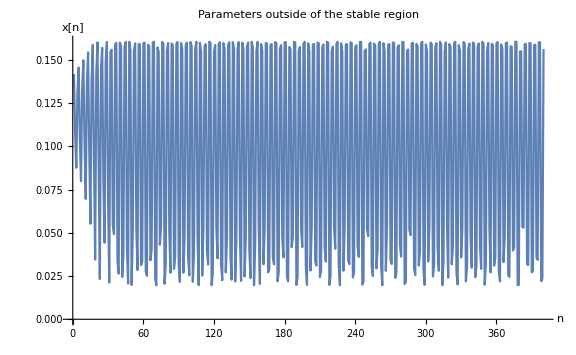

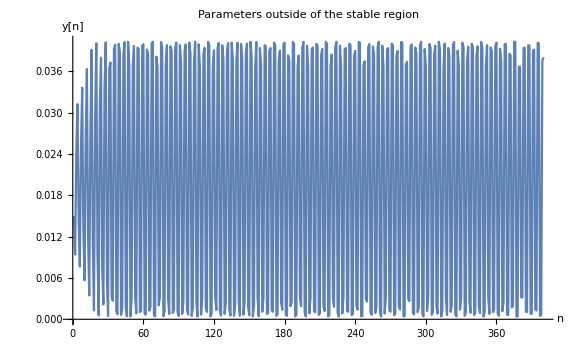

```mathematica
(*here I'm defining some functions,which will simplify further calculations*)(*this is the initial system with c1=1,and c2 is a parameter*)discF:=Function[{x[n+1],y[n+1]}=={Sqrt[y[n]]-y[n],Sqrt[x[n]/#]-x[n]}]

(*function for y-coordinate of equilibrium position*)
EqYF:=Function[1/(1+#)^2]

(*function for x-coordinate of equilibrium position*)
EqXF:=Function[#/(1+#)^2]

(*temporary value for c2*)
temp=6.2;
(*There are two figures below.Both figures show behaviour of the system with parameters outside of zone of asymptotic stability of equilibrium point*)

(*Simply I took c2 outside of the right border of interval and took the initial condition near equilibrium point*)

(*I'm plotting x[n] and y[n] separately,because there is no point to plot y(x) according to the initial meaning of the model*)

dataPoints=RecurrenceTable[{discF[temp],x[0]==EqXF[temp]+0.01,y[0]==EqYF[temp]+0.01},{x,y},{n,1,400}];

ListPlot[dataPoints[[;;,1]],Joined->True,ImageSize->Large,AxesLabel->{"n","x[n]"},PlotLabel->"Parameters outside of the stable region"]

ListPlot[dataPoints[[;;,2]],Joined->True,ImageSize->Large,AxesLabel->{"n","y[n]"},PlotLabel->"Parameters outside of the stable region"]
```

```mathematica
(*Here is manipulation for observing system behaviour with different parametrs*)(*We can see that there is no stability,when c2 became more then 5.8 approximately*)Manipulate[ListPlot[RecurrenceTable[{discF[temp],x[0]==EqXF[temp]+0.01,y[0]==EqYF[temp]+0.01},{x,y},{n,1,400}][[;;,1]],Joined->True,ImageSize->Large,AxesLabel->{"n","x[n]"},PlotLabel->"Behaivier of the sytem"],{temp,0.2,6,0.1}]
```

```mathematica
(*Bifurcation diagram*)(*On the y-axes I am plotting values of y[n],n in (Cut,Nodes)*)(*On the x-axes I am plotting values of c2,which stands for c2/c1 as long as c1=1*)(*On the graph below we definitely can see bifurcation neer 6*)Print[Style[WARNING,18,Red]]

Print[Style["Upper piece of code takes approximately 15 min on my laptop to compute",18,Red]]
(*
Nodes=300;
Cut=100;
b=Table[temp,{temp,0.2,6.5,0.01}];
(*for detailed graph*)
b1=Table[temp,{temp,6,6.7,0.001}];
a=Table[RecurrenceTable[{discF[temp],x[0]==0.01,y[0]==0.01},{x,y},{n,1,Nodes}][[;;,2]],{temp,0.2,6.5,0.01}];
a1=Table[RecurrenceTable[{discF[temp],x[0]==0.01,y[0]==0.01},{x,y},{n,1,Nodes}][[;;,2]],{temp,6,6.7,0.001}];
res={};
For[i=1,i<Length[b],i++,For[j=Cut,j<(Nodes),j++,AppendTo[res,{b[[i]],a[[i,j]]}]]]
ListPlot[res,ImageSize->Large,PlotStyle->AbsolutePointSize[.01],AxesLabel->{"c_2","y[n]"},PlotLabel->"Bifurcation diagram"]


res1={};

For[i=1,i<Length[b],i++,For[j=Cut,j<(Nodes),j++,AppendTo[res,{b[[i]],a1[[i,j]]}]]]

ListPlot[res1,ImageSize->Large,PlotStyle->AbsolutePointSize[.01],AxesLabel->{"c_2","y[n]"},PlotLabel->"Bifurcation diagram (near c_2 = 6)"]

*)
```

WARNING

Upper piece of code takes approximately 15 min on my laptop to compute

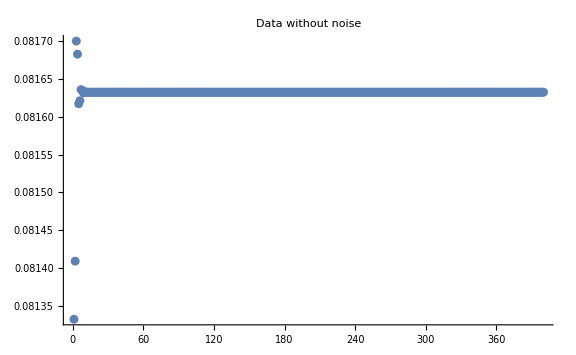

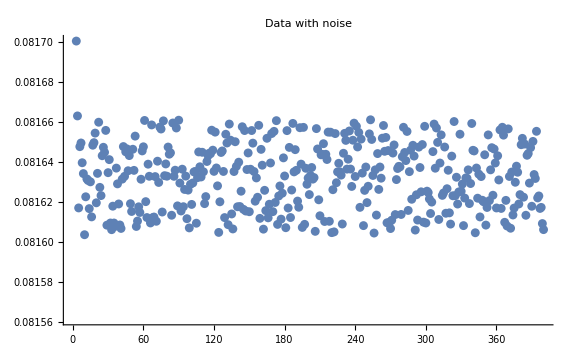

Even with this small modifications, system changes behaviour very 
dramatically

{{0.694078,-1.70111},{0.358662,-0.925687}}

Real parametrs{{1,-1},{2.5,-1}}

```mathematica
(*"Real" data*)(*temperary value of c2*)temp=2.5;
dataPoints=RecurrenceTable[{discF[temp],x[0]==EqXF[temp]+0.001,y[0]==EqYF[temp]+0.001},{x,y},{n,1,400}];

ListPlot[dataPoints[[;;,2]],Joined->False,ImageSize->Large,PlotLabel->"Data without noise"]

(*Adding noise to obtained data*)
(*I'm taking very small parameter before Mean value,because result even with 0.0002 is quite bad*)
(*I tried others,but system is very sensitive to noise*)
noizyDataPoints=Map[(#+RandomReal[{-0.0002 Mean[Abs[#]],0.0002 Mean[Abs[#]]},2])&,dataPoints];

ListPlot[noizyDataPoints[[;;,2]],Joined->False,ImageSize->Large,PlotLabel->"Data with noise"]
Print["Even with this small modifications, system changes behaviour very 
dramatically"]

X=noizyDataPoints[[;;-2,1]];
(*Subscript[x,n+1]*)
XStep=noizyDataPoints[[2;;,1]];
Y=noizyDataPoints[[;;-2,2]];
(*Subscript[y,n+1]*)
YStep=noizyDataPoints[[2;;,2]];

dataX={X,Y,XStep}ᵀ;
dataY={X,Y,YStep}ᵀ;

fit4X=FindFit[dataX,Sqrt[y/estC1]+estC2*y,{estC1,estC2},{x,y}];
fit4Y=FindFit[dataY,Sqrt[x*estC3]+estC4*x,{estC3,estC4},{x,y}];
estimatedM=({{estC1,estC2},{estC3,estC4}})/.fit4X/.fit4Y
Print["Real parametrs",{{1,-1},{temp,-1}}]
```

```mathematica
(*Obtained and initial parameters differ significantly.Even from the picture we can
see that this model is very sensitive for the noise and doubted is good for real-world data.*)
```